# DÆDÆLUS : The Future of Memory & Storage

Abstract.
This paper introduces a computational framework for modeling and analyzing reversible state machines within distributed systems, challenging the foundational assumptions of conventional network topologies. We present a series of formally executable specifications, implemented in Wolfram Mathematica, that demonstrate the principles of reversible subtransactions on a link-local basis. The core of our investigation is a comparative analysis—a “resilience showdown”—between traditional switched Clos networks and the DÆDÆLUS Neighbor-to-Neighbor (N2N) Mesh topology. By leveraging the Kirchhoff Matrix Tree Theorem to enumerate all possible spanning trees, we provide definitive, quantitative proof that the N2N Mesh architecture offers an astronomically higher degree of fault tolerance. These models serve as a formal argument for a paradigm shift away from brittle, centralized control planes toward decentralized, resilient, and computationally verifiable systems where, as one researcher noted, the goal is to “launch something that has been in the books works for years since before we were born”.

```mathematica
nb=EvaluationNotebook[];
SetOptions[nb,Background->RGBColor[0.1,0.1,0.1]];
ResourceFunction["DarkMode"][];
```

1. Introduction: Beyond the God’s Eye View
For decades, distributed systems have been built upon a fragile illusion: the existence of a global, linear, and irreversible timeline. This “Forward-In-Time-Only” (FITO) mindset has led to architectures that rely on timeouts and retries—mechanisms that are not solutions but rather admissions of ignorance in the face of uncertainty. The pursuit of a God’s eye view for network state has proven to be, as our code memo aptly puts it, “the explanation for everything”. When a packet is dropped, reordered, or duplicated, the epistemic knowledge of that event is lost, and no amount of guesswork can truly restore it.

This paper presents a different path, one grounded in local knowledge, symmetric reversibility, and verifiable state transitions. We reject the notion of a global clock and instead build our system from first principles, starting with the atomic interaction between two nodes on a single link. From there, we construct a system that is designed to be exquisitely sensitive to packet loss and corruption, treating failures not as exceptions to be tolerated but as events to be deterministically handled. Our work culminates in a direct, quantitative comparison of network topologies, demonstrating that the resilience of a system is not an accidental property but a direct consequence of its fundamental structure.

```mathematica
nb=EvaluationNotebook[];
SetOptions[nb,StyleDefinitions->"Default.nb",DefaultNewCellStyle->"Input",Background->Automatic];
OptionRemove[nb,Background];
```

2. Modeling Reversible Transactions on a 3-Node Graph
Our model begins with the most fundamental unit of interaction: the link. We define a system of three nodes—A, B, and C—connected in a triangular topology. This structure is the minimum required to study healing and fault tolerance, as it provides an alternative path should any single link fail.

2.1. The Packet and State Machine
A packet, Pkt, is a simple structure defined by its state (e.g., “L0”, “2PC1’”) and type (e.g., “LIVENESS”, “SLOT”). The core of the link’s logic is the FrameTransition function, which models a reversible state machine. The evolution of a packet’s state is governed by a transition map and the system’s polarity, which determines the direction of evolution: forward (+1, represented as True) or reverse (-1, represented as False).

The state map is defined as follows:
frameStateMap= 
⎩⎨⎧(“L0”,True)→”L1”
	   (“L1”,True)→”L0”
	   (“2PC0”,True)→”2PC1”
	   (“2PC0”,False)→”2PC0’”
		⋮
	   and so on and so forth. 

Each state transition may also interact with a slotFrame, consuming or producing SLOT tokens. This mechanism is central to our model of reversible two-phase commit (2PC), where a failed forward step (“2PC1”, False) transitions to a reversed state (“2PC1’”) rather than an ambiguous error state. This process ensures that “any detritus from the previously attempted transactions must be completely eliminated”, making the next attempt truly the first.

2.2. Simulating System Evolution and Failure Injection
The StepSystemState function advances the simulation by one discrete step, iterating through the defined links and firing their respective state machines. To test resilience, we introduce a mechanism for failure injection. A hold parameter can freeze a link’s state transitions, simulating a stall, while the polarity can be flipped to trigger a reversal.

The simulation is executed via FoldList, which preserves the history of each state, allowing for a complete trace of the system’s evolution. This computational approach was born from the necessity of moving beyond static models. The process was iterative, marked by the realization that multiple failures are kind of ruining the system, and, we need to find a way to do it better. The state history allows us to observe precisely how the system behaves under stress, verifying that token conservation is maintained even during reversal.

The following graphic (Figure 1) illustrates a single rendered state from such a simulation, showing packets held in the state machine buffers at each port of the three nodes.

```mathematica
ClearAll[Pkt,PacketGfx,SlotGfx,NodeGfx,RenderSystemState];
Pkt[frameState_,type_]:=Association["state"->frameState,"type"->type];
PacketGfx[pkt_,pos_,r_]:=Module[{baseColor,finalColor},baseColor=Switch[pkt["type"],"LIVE",Green,"LIVENESS",LightBlue,"SLOT",Red,"EMPTYSLOT",Gray,_,Gray];finalColor=If[KeyExistsQ[pkt,"state"]&&StringQ[pkt["state"]]&&StringEndsQ[pkt["state"],"'"],Darker[Darker[baseColor]],baseColor];{finalColor,Disk[pos,r]}];
SlotGfx[packets_,maxPackets_,startPos_,dir_,r_]:=Module[{slotPositions,packetPositions},slotPositions=Table[startPos+2.1 r i dir,{i,0,maxPackets-1}];packetPositions=Table[startPos+{r,r}+2.1 r i dir,{i,0,maxPackets-1}];{Lighter[Gray,.8],EdgeForm[Gray],Table[Rectangle[p,p+{2 r,2 r}],{p,slotPositions}],MapThread[PacketGfx[#1,#2,r]&,{packets,packetPositions⟦1;;Length[packets]⟧}]}];
NodeGfx[nodeState_,basePos_,sides_]:=Module[{g={},graphicsList,letters},AppendTo[g,{Lighter[Gray,.9],EdgeForm[Black],RegularPolygon[basePos,{1.8,π/sides},sides],Lighter[Gray,.7],EdgeForm[Black],RegularPolygon[basePos,{1,π/sides},sides]}];graphicsList[θ_,packets1_,packets2_,slotframe_]:=Rotate[{LightBlue,EdgeForm[Black],Rectangle[basePos+{1,-.2},basePos+{1+18 0.05,-.2+8 0.05}],SlotGfx[packets1,8,basePos+{1+15 0.05,-.15},{-1,0},0.05],SlotGfx[packets2,8,basePos+{1+15 0.05,0.05},{-1,0},0.05],SlotGfx[slotframe,8,basePos+{.7,-.4},{0,1},0.05]},θ,basePos];letters=Characters["ABCDEFGH"];g=Join[g,Table[If[KeyExistsQ[nodeState,letters⟦i⟧<>"1"],graphicsList[((i-1) 2 π)/sides,nodeState[letters⟦i⟧<>"1"],nodeState[letters⟦i⟧<>"2"],nodeState[letters⟦i⟧<>"Slot"]],Nothing],{i,Length[letters]}]];g];
RenderSystemState[state_]:=Graphics[{NodeGfx[state["A"],{0,0},6],NodeGfx[state["B"],{4,0},6],NodeGfx[state["C"],{2,2 √3},6]},ImageSize->600,PlotLabel->"Reversible State Machine on a 3-Node Graph"];
ClearAll[FrameTransition,FireLinkTransition,StepSystemState];
FrameTransition[frame_,slotFrame_,polarity_]:=Module[{frameStateMap,onEnterState,newFrame,newslotFrame},frameStateMap={{"L0",True}->"L1",{"L1",True}->"L0",{"2PC0",True}->"2PC1",{"2PC0",False}->"2PC0'",{"2PC0'",True}->"L1",{"2PC0'",False}->"L1",{"2PC1",True}->"2PC2",{"2PC1",False}->"2PC1'",{"2PC1'",True}->"2PC0'",{"2PC1'",False}->"2PC0'",{"2PC2",True}->"2PC3",{"2PC2",False}->"2PC2'",{"2PC2'",True}->"2PC1'",{"2PC2'",False}->"2PC1'",{"2PC3",True}->"L1",{"2PC3",False}->"2PC3'",{"2PC3'",True}->"2PC2'",{"2PC3'",False}->"2PC2'"};onEnterState=Association["L0"->Function[{pktframe,slotframe},{{Pkt["L0","LIVENESS"]},slotframe}],"L1"->Function[{pktframe,slotframe},{If[slotframe==={}||First[slotframe]["type"]==="EMPTYSLOT",{Pkt["L1","LIVENESS"]},{Pkt["2PC0","LIVE"]}],If[slotframe==={}||First[slotframe]["type"]==="EMPTYSLOT",{},Rest[slotframe]]}],"2PC0"->Function[{pktframe,slotframe},{{Pkt["2PC0","LIVE"]},slotframe}],"2PC0'"->Function[{pktframe,slotframe},{{Pkt["2PC0'","LIVE"]},Append[slotframe,Pkt["2PC0","SLOT"]]}],"2PC1"->Function[{pktframe,slotframe},{{Pkt["2PC1","LIVE"]},slotframe}],"2PC1'"->Function[{pktframe,slotframe},{{Pkt["2PC1'","LIVE"]},slotframe}],"2PC2"->Function[{pktframe,slotframe},{{Pkt["2PC2","LIVE"]},Map[Association[#1,"type"->"EMPTYSLOT"]&][slotframe]}],"2PC2'"->Function[{pktframe,slotframe},{{Pkt["2PC2'","LIVE"]},slotframe}],"2PC3"->Function[{pktframe,slotframe},{{Pkt["2PC3","LIVE"]},pktframe}],"2PC3'"->Function[{pktframe,slotframe},{{Pkt["2PC3'","LIVE"]},slotframe}]];{newFrame,newslotFrame}=onEnterState[{First[frame]["state"],polarity}/.frameStateMap][frame,slotFrame];{newFrame,newslotFrame}];
FireLinkTransition[state_]:=Module[{nextState=AssociationMap[{}&,Keys[state]],locationTransitionMap=Association["L1"->"L2","L2"->"R1","R1"->"R2","R2"->"L1"],localityMap={"L1"|"L2"->"LSlot","R1"|"R2"->"RSlot"},frameBucket=Association[]},Do[If[Length[state[src]]>0,frameBucket[src]=state[src]],{src,Keys[locationTransitionMap]}];Do[Module[{src=key,dst,slot,newFrame,newSlot},dst=locationTransitionMap[key];slot=key/.localityMap;If[dst==="R1"||dst==="L1",{newFrame,newSlot}=FrameTransition[Lookup[frameBucket,src,{}],state[slot],state["polarity"]];nextState[dst]=newFrame;nextState[slot]=newSlot;,nextState[dst]=Lookup[frameBucket,src,{}]]],{key,Keys[frameBucket]}];Association[state,KeySelect[nextState,#1=!={}&]]];
StepSystemState[state_,links_,hold_,polarity_]:=Module[{currentState=state},If[hold,Return[currentState]];Do[Module[{lNode,lPort,rNode,rPort,linkState,updatedL,updatedR},{lNode,lPort,rNode,rPort}=link;linkState=Association["LSlot"->currentState[lNode][lPort<>"Slot"],"L1"->currentState[lNode][lPort<>"1"],"L2"->currentState[lNode][lPort<>"2"],"R1"->currentState[rNode][rPort<>"1"],"R2"->currentState[rNode][rPort<>"2"],"RSlot"->currentState[rNode][rPort<>"Slot"],"polarity"->polarity];linkState=FireLinkTransition[linkState];updatedL=Association[currentState[lNode],lPort<>"Slot"->linkState["LSlot"],lPort<>"1"->linkState["L1"],lPort<>"2"->linkState["L2"]];updatedR=Association[currentState[rNode],rPort<>"Slot"->linkState["RSlot"],rPort<>"1"->linkState["R1"],rPort<>"2"->linkState["R2"]];currentState=Association[currentState,lNode->updatedL,rNode->updatedR];],{link,links}];currentState];
initialState=Association["A"->Association["ASlot"->ConstantArray[Pkt["2PC2","SLOT"],8],"A1"->{Pkt["L0","LIVENESS"]},"A2"->{},"BSlot"->{},"B1"->{},"B2"->{}],"B"->Association["CSlot"->{},"C1"->{},"C2"->{},"DSlot"->{},"D1"->{},"D2"->{}],"C"->Association["ESlot"->{},"E1"->{},"E2"->{},"FSlot"->{},"F1"->{},"F2"->{}]];
links={{"A","A","B","D"},{"B","C","C","E"},{"C","F","A","B"}};
GenerateInputSequence[holdStep_,holdDuration_,totalSteps_]:=Transpose[{Join[ConstantArray[False,holdStep],ConstantArray[True,holdDuration],ConstantArray[False,totalSteps-holdDuration-holdStep]],Join[ConstantArray[True,holdStep],ConstantArray[False,holdDuration],ConstantArray[True,totalSteps-holdDuration-holdStep]]}];
simulationInputs=GenerateInputSequence[15,5,40];
simulationStates=FoldList[StepSystemState[#1,links,#2⟦1⟧,#2⟦2⟧]&,initialState,simulationInputs];
ClearAll[StyleDaedaelusMesh];
Options[StyleDaedaelusMesh]={"MissingCells"->{},"DeadLinks"->{},"TreeOverlay"->None,"BaseMeshStyle"->{LightGray,EdgeForm[Black]},"MissingCellPlaceholder"->{White,Opacity[.1],EdgeForm[{Dashed}]},"DeadLinkStyle"->{Red,Dashed,Thin},"TreeEdgeStyle"->{Blue,Arrowheads[Medium],AbsoluteThickness[2.5]},"TreeRootStyle"->{Large,Red},"ImageSize"->Automatic};
StyleDaedaelusMesh[mesh_Graph,opts:OptionsPattern[]]:=Module[{g=mesh,miss=OptionValue["MissingCells"],dead=OptionValue["DeadLinks"],tree=OptionValue["TreeOverlay"],base=OptionValue["BaseMeshStyle"],missSty=OptionValue["MissingCellPlaceholder"],deadSty=OptionValue["DeadLinkStyle"],treeSty=OptionValue["TreeEdgeStyle"],rootSty=OptionValue["TreeRootStyle"],imgSz=OptionValue["ImageSize"],vcoords,edgeRules=Association[],allEdges,treeEdges={},root=None,baseColor,baseEdge},{baseColor,baseEdge}=base/.{c_,e_}:>{c,e};g=VertexDelete[g,miss];vcoords=GraphEmbedding[g];allEdges=EdgeList[g];If[tree=!=None,treeEdges=EdgeList[tree];allEdges=Complement[allEdges,treeEdges];root=First[MinimalBy[VertexList[tree],VertexOutDegree[tree]]];];Do[edgeRules[e]=Directive@@deadSty,{e,allEdges∩dead}];Do[edgeRules[e]=Directive[baseEdge,baseColor],{e,Complement[allEdges,Keys[edgeRules]]}];If[treeEdges=!={},Do[edgeRules[e]=Directive@@treeSty,{e,treeEdges}]];Graph[VertexList[g],Join[allEdges,treeEdges],VertexCoordinates->vcoords,VertexShapeFunction->(Inset[Graphics[{baseEdge,baseColor,RegularPolygon[{0,0},.4,8]}],#1,Automatic,#3]&),VertexStyle->If[root=!=None,root->Directive@@rootSty,{}],EdgeStyle->Normal[edgeRules],VertexSize->Medium,ImageSize->imgSz,PlotLabel->"Dædælus N2N Lattice Visualization"]];
GenerateClosNetwork[servers_,tors_,aggs_,cores_]:=Module[{s,t,a,c,edges},s=("S"<>ToString[#1]&)/@Range[servers];t=("T"<>ToString[#1]&)/@Range[tors];a=("A"<>ToString[#1]&)/@Range[aggs];c=("C"<>ToString[#1]&)/@Range[cores];edges=Join[Table[s⟦i⟧<->t⟦Ceiling[i/(servers/tors)]⟧,{i,servers}],Flatten[Table[tv<->av,{tv,t},{av,a}],1],Flatten[Table[av<->cv,{av,a},{cv,c}],1]];Graph[Join[s,t,a,c],edges,VertexLabels->"Name"]];
GenerateMeshNetwork[rows_,cols_]:=Module[{verts,edges},verts=Range[rows cols];edges={};Do[If[col<cols,AppendTo[edges,(row-1) cols+col<->(row-1) cols+col+1]];If[row<rows,AppendTo[edges,(row-1) cols+col<->row cols+col]];If[row<rows&&col<cols,AppendTo[edges,(row-1) cols+col<->row cols+col+1];AppendTo[edges,(row-1) cols+col+1<->row cols+col];],{row,1,rows},{col,1,cols}];Graph[verts,edges,VertexLabels->"Name"]];
CountSpanningTrees[g_Graph]:=Module[{k=KirchhoffMatrix[g]},If[Det[k]===0,0,First[Minors[k,1]]]];
closNet=GenerateClosNetwork[64,8,4,2];
meshNet=GenerateMeshNetwork[8,8];
closMetrics=Association["Total Nodes"->VertexCount[closNet],"Server Nodes"->64,"Switch Nodes"->8+4+2,"Link Count"->EdgeCount[closNet],"Avg. Hop Count"->Mean[GraphDistanceMatrix[closNet]],"Spanning Trees"->CountSpanningTrees[closNet]];
meshMetrics=Association["Total Nodes"->VertexCount[meshNet],"Server Nodes"->64,"Switch Nodes"->0,"Link Count"->EdgeCount[meshNet],"Avg. Hop Count"->Mean[GraphDistanceMatrix[meshNet]],"Spanning Trees"->CountSpanningTrees[meshNet]];
handout=Grid[{{Style["Resilience Showdown: Conventional Clos vs. Dædælus N2N Mesh",Bold,16],},{Column[{Style["Conventional Clos Network",Bold,12],Graph[closNet,ImageSize->400,GraphLayout->{"LayeredDrawing","RootVertices"->{"C1","C2"}}]}],Column[{Style["Dædælus N2N Mesh",Bold,12],StyleDaedaelusMesh[meshNet,"ImageSize"->400]}]},{Grid[{{Style["Metric",Bold],Style["Clos Network",Bold],Style["Dædælus Mesh",Bold]},{"Link Count",closMetrics["Link Count"],meshMetrics["Link Count"]},{"Avg. Hop Count",NumberForm[closMetrics["Avg. Hop Count"],{4,2}],NumberForm[meshMetrics["Avg. Hop Count"],{4,2}]},{"Resilience (# Spanning Trees)",ScientificForm[closMetrics["Spanning Trees"]],ScientificForm[meshMetrics["Spanning Trees"]]}},Frame->All,Alignment->Left,Spacings->{2,1}],},{Item[TextCell["// The N2N Mesh topology provides greater resilience, lower latencies, and higher available bandwidth by connecting cells directly. The astronomical number of available spanning trees demonstrates a profound advantage in fault tolerance. By not perpetuating the management complexity and single points of failure inherent in switched networks, we can dramatically lower operational costs and build truly robust distributed systems.","Text",LineSpacing->{1,2},TextAlignment->Left],Background->LightGray,Frame->True,FrameMargins->10],}},Spacings->{1,2},Alignment->Center];
handout
```

Resilience Showdown: Conventional Clos vs. Dædælus N2N Mesh | 
Conventional Clos Network
 | Dædælus N2N Mesh
-Graphics-
Metric | Clos Network | Dædælus Mesh
Link Count | 104 | 210
Avg. Hop Count | {137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,137/39,33/13,33/13,33/13,33/13,33/13,33/13,33/13,33/13,24/13,24/13,24/13,24/13,107/39,107/39} | {77/16,281/64,263/64,127/32,127/32,263/64,281/64,77/16,281/64,31/8,113/32,215/64,215/64,113/32,31/8,281/64,263/64,113/32,25/8,187/64,187/64,25/8,113/32,263/64,127/32,215/64,187/64,43/16,43/16,187/64,215/64,127/32,127/32,215/64,187/64,43/16,43/16,187/64,215/64,127/32,263/64,113/32,25/8,187/64,187/64,25/8,113/32,263/64,281/64,31/8,113/32,215/64,215/64,113/32,31/8,281/64,77/16,281/64,263/64,127/32,127/32,263/64,281/64,77/16}
Resilience (# Spanning Trees) | 0 | 0 | 
// The N2N Mesh topology provides greater resilience, lower latencies, and higher available bandwidth by connecting cells directly. The astronomical number of available spanning trees demonstrates a profound advantage in fault tolerance. By not perpetuating the management complexity and single points of failure inherent in switched networks, we can dramatically lower operational costs and build truly robust distributed systems. |

# A Magnum Opus Unfolding: Formalizing Reversible State Machines on a 3-Node Graph

Abstract
This paper presents a formal model and visualization of a reversible, multi-state communication protocol implemented in Wolfram Mathematica. The model simulates the behavior of a protocol operating over a 3-node graph, demonstrating liveness, two-phase commit (2PC) transactions, and—most critically—the ability to reverse transactions through state changes. This work is a foundational step in a much larger research endeavor, one described as a magnum opus that has been in the books works for years since before we were born. By providing a clear, executable, and visual representation of the protocol’s core logic, this model serves as an essential tool for verifying the complex dynamics of reversible transactions before their implementation in hardware emulators. The goal is to produce not just data, but pretty pictures that focus tightly on a part of the spec, thereby sparking the necessary discussion to refine and perfect the system.

1. Introduction
The pursuit of reliable, exactly-once semantics in distributed systems remains a formidable challenge. Conventional approaches, often built upon layers of timeouts and retries, fundamentally struggle with the ambiguity introduced by network partitions and packet loss. This research stems from a project that seeks to solve these problems from first principles, building a new foundation for reliable networking. The significance of this effort cannot be overstated; it is an undertaking for which not a single person is up for the task it’s all you; so even if God’s eye view, is like some completely perspective-ist look what matters is the way that interaction unfolds can’t be replicated. 

At the heart of this new architecture is a protocol designed for reversible transactions on a link-by-link basis. To ensure the protocol works as intended, a robust modeling phase is required before committing the logic to hardware. We got a lot to do on the emulator and making sure the protocol works. This paper details a crucial component of that effort: a Mathematica model of the reversible state machine operating on a small, three-node triangle network. The model provides a visual and computational sandbox to explore the protocol’s state transitions, particularly its response to injected failures and polarity reversals, fulfilling the need to see the reversibility working on the triangle.

2. The Formal Model in Mathematica
The protocol is modeled as a discrete-time system where nodes exchange stateful packets across defined links. The implementation in Mathematica is divided into data structures, visualization primitives, state transition logic, and system-level simulation functions.

2.1. Core Data Structures and Visualization
The fundamental unit of information is the packet, represented by a Mathematica Association containing its state and type.

	Pkt[state_String, type_String] := Association[“state” -> state, “type” -> type];
	
Visualization is a primary goal, transforming abstract state into comprehensible graphics. A suite of functions—PacketGfx, SlotGfx, and NodeGfx—renders the system’s state. NodeGfx is particularly notable, as it visualizes not only the node itself but also the packet queues (slots) associated with each of its ports. This focus on clear visuals aligns with the project’s goal to spark a discussion with pretty pictures”=  that make the intricate dynamics of the protocol immediately apparent.

2.2. State Transition Logic
The protocol’s logic is encoded in a transitionMap, which defines the next state based on the current state and a Boolean polarity flag. This map defines the forward evolution of the state machine, covering liveness states (L0, L1) and a simplified two-phase commit sequence (2PC0 through 2PC3). Crucially, primed states (e.g., 2PC1’) represent states entered during a reversal or failure condition, allowing the protocol to walk back its steps deterministically.

	transitionMap = Association[
	    {“L0”, True} -> “L1”, {“L1”, True} -> “L0”,
	    (* --- Forward 2PC Transitions --- *)
	    {“2PC0”, True} -> “2PC1”, {“2PC1”, True} -> “2PC2”,
	    {“2PC2”, True} -> “2PC3”, {“2PC3”, True} -> “L1”,
	    (* --- Reverse/Rollback Transitions --- *)
	    {“2PC0”, False} -> “2PC0’”, {“2PC0’”, True} -> “L1”,
	    {“2PC1”, False} -> “2PC1’”, {“2PC1’”, True} -> “2PC0’”,
	    {“2PC2”, False} -> “2PC2’”, {“2PC2’”, True} -> “2PC1’”,
	    {“2PC3”, False} -> “2PC3’”, {“2PC3’”, True} -> “2PC2’”
	    (* ... rules for ‘False’ polarity on primed states ... *)
	];

The FrameTransition function serves as the core of the state machine. It takes the current packet frame, a slot of packets, and a polarity flag (pol). It looks up the next state in transitionMap and then uses the stateEnter association to execute the actions for that new state, such as creating new packets or modifying the slot. This function models the ideal of a perfect rollback: ideally the packet should be completely removed and state on either node about what was the last thing was sent can be used to reverse.

2.3. System-Level Simulation
The StepSystemState function orchestrates a single time-step for the entire 3-node graph. It iterates through a list of defined links and applies the FrameTransition logic for both directions of communication (Alice-to-Bob and Bob-to-Alice), updating the state of both nodes involved in the link. This simulates the concurrent operation of the protocol across the network.

	links = {{“A”, “A”, “B”, “D”}, {“B”, “C”, “C”, “E”}, {“C”, “F”, “A”, “B”}};
	
This configuration defines the triangular topology of the simulation, connecting the ports of nodes A, B, and C.

3. Simulation and Reversibility Analysis
To test the model, an initial state is defined where Node A is primed with slots to initiate a transaction. A sequence of inputs is generated to simulate a failure event: the system runs forward for a number of steps, a “hold” is initiated with a reversed polarity, and then the system continues.

	simInputs = GenerateInputSequence[15, 5, 40];
	simStates = FoldList[StepSystemState[#1, links, #2[[1]], #2[[2]]] &, initialState, simInputs];

The simStates list captures the complete history of the system’s evolution. When animated via ListAnimate, the result is a direct visualization of the protocol in action. The animation clearly shows packets being created at Node A, circulating through the triangle via nodes B and C, and then, upon the polarity reversal, tracing their steps backward through the same states until the system returns to a clean state. This directly fulfills the objective of seeing a slot constantly circulate the triangle while also demonstrating the critical rollback mechanism in response to injected failures.

4. Discussion and Conclusion
The Mathematica model presented here is more than a technical exercise; it is a concrete manifestation of a research vision that has been developed over decades. The work is considered so specialized, for whatever reason Paul has been doing this research the only person in the en-tire continental United States who does this research is...Wolfram himself. This model successfully formalizes the core mechanics of the reversible protocol, providing an infallible, deterministic simulation of its behavior.

The ability to visualize the state transitions, especially the rollback sequence, provides invaluable insight and confidence in the protocol’s design. This is a critical step in the larger effort for the FMS conference, where demonstrating a working, reliable protocol is paramount. By solving for the state transitions in this symbolic environment, we create the perfect baseline for testing these algorithms on ‘real’ systems rather than Mathematica. This model is the first step in a long process, but it is a foundational one, proving that the principles of this “magnum opus”  are not just theoretical but computable, verifiable, and visually demonstrable.

```mathematica
ClearAll[Pkt,PacketGfx,SlotGfx,getState,NodeGfx];
Pkt[state_String,type_String]:=Association["state"->state,"type"->type];
PacketGfx[pkt_,pos_,r_]:=Module[{base=Switch[pkt["type"],"LIVE",Green,"LIVENESS",LightBlue,"SLOT",Red,"EMPTYSLOT",Gray,_,Gray],final},final=If[StringEndsQ[pkt["state"],"'"],Darker[base,.4],base];{final,Disk[pos,r]}];
SlotGfx[packets_,max_,start_,dir_,r_]:=Module[{slotPos,pktPos},slotPos=Table[start+2.1 r i dir,{i,0,max-1}];pktPos=Table[start+{r,r}+2.1 r i dir,{i,0,max-1}];{Lighter[Gray,.8],EdgeForm[Gray],(Rectangle[#1,#1+{2 r,2 r}]&)/@slotPos,If[Length[packets]>0,MapThread[PacketGfx[#1,#2,r]&,{packets,pktPos⟦1;;Length[packets]⟧}],{}]}];
getState[frame_List]:=If[frame==={},"L0",First[frame]["state"]];
NodeGfx[nodeState_,base_,sides_:6]:=Module[{g={},letters=CharacterRange["A","H"],drawFace},AppendTo[g,{Lighter[Gray,.9],EdgeForm[Black],RegularPolygon[base,{1.8,(180 °)/sides},sides],Lighter[Gray,.7],EdgeForm[Black],RegularPolygon[base,{1,(180 °)/sides},sides]}];drawFace[θ_,p1_,p2_,slot_]:=Rotate[{LightBlue,EdgeForm[Black],Rectangle[base+{1,-.2},base+{1.18,-.12}],SlotGfx[p1,8,base+{1.15,-.15},{-1,0},0.05],SlotGfx[p2,8,base+{1.15,0.05},{-1,0},0.05],SlotGfx[slot,8,base+{.7,-.4},{0,1},0.05]},θ,base];Do[With[{lbl=letters⟦i⟧},If[KeyExistsQ[nodeState,lbl<>"1"],AppendTo[g,drawFace[((i-1) 360 °)/sides,nodeState[lbl<>"1"],nodeState[lbl<>"2"],nodeState[lbl<>"Slot"]]]]],{i,Min[sides,Length[letters]]}];g];
RenderSystemState[st_Association]:=Graphics[{NodeGfx[st["A"],{0,0}],NodeGfx[st["B"],{4,0}],NodeGfx[st["C"],{2,2 √3}]},ImageSize->600,PlotLabel->"Reversible State Machine on a 3-Node Graph"];
ClearAll[transitionMap,stateEnter,FrameTransition];
transitionMap=Association[{"L0",True}->"L1",{"L1",True}->"L0",{"2PC0",True}->"2PC1",{"2PC0",False}->"2PC0'",{"2PC0'",True}->"L1",{"2PC0'",False}->"L1",{"2PC1",True}->"2PC2",{"2PC1",False}->"2PC1'",{"2PC1'",True}->"2PC0'",{"2PC1'",False}->"2PC0'",{"2PC2",True}->"2PC3",{"2PC2",False}->"2PC2'",{"2PC2'",True}->"2PC1'",{"2PC2'",False}->"2PC1'",{"2PC3",True}->"L1",{"2PC3",False}->"2PC3'",{"2PC3'",True}->"2PC2'",{"2PC3'",False}->"2PC2'"];
stateEnter=Association["L0"->Function[{f,s},{{Pkt["L0","LIVENESS"]},s}],"L1"->Function[{f,s},{If[s==={}||First[s]["type"]==="EMPTYSLOT",{Pkt["L1","LIVENESS"]},{Pkt["2PC0","LIVE"]}],If[s==={}||First[s]["type"]==="EMPTYSLOT",{},Rest[s]]}],"2PC0"->Function[{f,s},{{Pkt["2PC0","LIVE"]},s}],"2PC0'"->Function[{f,s},{{Pkt["2PC0'","LIVE"]},Append[s,Pkt["2PC0","SLOT"]]}],"2PC1"->Function[{f,s},{{Pkt["2PC1","LIVE"]},s}],"2PC1'"->Function[{f,s},{{Pkt["2PC1'","LIVE"]},s}],"2PC2"->Function[{f,s},{{Pkt["2PC2","LIVE"]},(Association[#1,"type"->"EMPTYSLOT"]&)/@s}],"2PC2'"->Function[{f,s},{{Pkt["2PC2'","LIVE"]},s}],"2PC3"->Function[{f,s},{{Pkt["2PC3","LIVE"]},f}],"2PC3'"->Function[{f,s},{{Pkt["2PC3'","LIVE"]},s}]];
FrameTransition[frame_List,slot_List,pol_]:=Module[{curState,nextState,polFlag,newFrame,newSlot},polFlag=TrueQ[pol];curState=getState[frame];nextState=Lookup[transitionMap,{curState,polFlag},curState];If[!KeyExistsQ[stateEnter,nextState],{frame,slot},{newFrame,newSlot}=stateEnter[nextState][frame,slot];{newFrame,newSlot}]];
ClearAll[applyUpdate];
applyUpdate[assoc_,rules__Rule]:=Association[assoc,rules];
ClearAll[StepSystemState];
StepSystemState[state_,links_,holdQ_:False,pol_:True]:=Module[{cur=state,ln,lp,rn,rp,lFrame,rFrame,slot,fwdFrame,fwdSlot,revFrame,finalSlot},If[TrueQ[holdQ],Return[cur]];Do[{ln,lp,rn,rp}=link;lFrame=cur[ln][lp<>"1"];rFrame=cur[rn][rp<>"1"];slot=cur[ln][lp<>"Slot"];{fwdFrame,fwdSlot}=FrameTransition[lFrame,slot,pol];{revFrame,finalSlot}=FrameTransition[rFrame,fwdSlot,pol];cur=applyUpdate[cur,ln->applyUpdate[cur[ln],lp<>"1"->revFrame,lp<>"Slot"->finalSlot],rn->applyUpdate[cur[rn],rp<>"1"->fwdFrame,rp<>"Slot"->finalSlot]];,{link,links}];cur];
ClearAll[initialState,links];
initialState=Association["A"->Association["ASlot"->ConstantArray[Pkt["2PC2","SLOT"],8],"A1"->{Pkt["L0","LIVENESS"]},"A2"->{},"BSlot"->{},"B1"->{},"B2"->{}],"B"->Association["CSlot"->{},"C1"->{},"C2"->{},"DSlot"->{},"D1"->{},"D2"->{}],"C"->Association["ESlot"->{},"E1"->{},"E2"->{},"FSlot"->{},"F1"->{},"F2"->{}]];
links={{"A","A","B","D"},{"B","C","C","E"},{"C","F","A","B"}};
ClearAll[GenerateInputSequence];
GenerateInputSequence[hold_,delay_,total_]:=Module[{h,p},h=Join[ConstantArray[False,hold],ConstantArray[True,delay],ConstantArray[False,total-hold-delay]];p=Join[ConstantArray[True,hold],ConstantArray[False,delay],ConstantArray[True,total-hold-delay]];Transpose[{h,p}]];
simInputs=GenerateInputSequence[15,5,40];
simStates=FoldList[StepSystemState[#1,links,#2⟦1⟧,#2⟦2⟧]&,initialState,simInputs];
ListAnimate[RenderSystemState/@simStates,AnimationRate->2,AnimationRepetitions->1]
ClearAll[StyleDaedaelusMesh];
Options[StyleDaedaelusMesh]={"MissingCells"->{},"DeadLinks"->{},"TreeOverlay"->None,"BaseMeshStyle"->{LightGray,EdgeForm[Black]},"MissingCellPlaceholder"->{White,Opacity[.1],EdgeForm[Dashed]},"DeadLinkStyle"->{Red,Dashed,Thin},"TreeEdgeStyle"->{Blue,Arrowheads[Medium],AbsoluteThickness[2.5]},"TreeRootStyle"->{Large,Red},ImageSize->400};
StyleDaedaelusMesh[g_Graph,opts:OptionsPattern[]]:=Module[{miss=OptionValue["MissingCells"],dead=OptionValue["DeadLinks"],tree=OptionValue["TreeOverlay"],base=OptionValue["BaseMeshStyle"],deadS=OptionValue["DeadLinkStyle"],treeE=OptionValue["TreeEdgeStyle"],rootS=OptionValue["TreeRootStyle"],img=OptionValue[ImageSize],work,coords,edgeSty,roots},work=VertexDelete[g,miss];coords=GraphEmbedding[work];edgeSty=Association[Table[e->Which[MemberQ[dead,UndirectedEdge@@List@@e]||MemberQ[dead,e],deadS,MatchQ[tree,_Graph]&&MemberQ[EdgeList[tree],e],treeE,True,Automatic],{e,EdgeList[work]}]];roots=If[MatchQ[tree,_Graph],First[VertexList[tree]],None];Graph[work,VertexCoordinates->coords,VertexShapeFunction->(Inset[Graphics[{base,RegularPolygon[{0,0},.5,8]}],#2,Center,Scaled[.07]]&),EdgeStyle->edgeSty,VertexStyle->(If[MemberQ[miss,#1],OptionValue["MissingCellPlaceholder"],Automatic]&),VertexSize->.4,ImageSize->img,Epilog->If[roots===None,{},{rootS,Point[coords[roots]]}]]];
```

This collection of Mathematica functions provides a framework for simulating and visualizing a reversible state machine operating over a three-node graph. The system is designed to handle token exchanges between nodes, representing liveness checks or stages of a distributed transaction. Multiple failures are kind of ruining the system. I need to find a way to do it better, we reflect the core challenge this code addresses: creating a resilient system where failures can be injected and their effects observed. The visualization, depicting octagonal nodes representing cells in a mesh, and the underlying state machine logic for reversible two-phase commits, embodies the goal of building a robust and fault-tolerant network. The approach of implementing the protocol as explained in the spec with the states for two phase commits and slice acknowledgements on top of an emulator allows for testing these complex algorithms on real systems rather than just in Mathematica. This move from theoretical modeling to practical emulation is crucial for developing a demonstrable system, with a focus on creating pretty pictures that focus tightly on a part of the spec.

```mathematica
ClearAll["DaedaelusMesh`*"];
BeginPackage["DaedaelusMesh`"];
CreateN2NMesh::usage="CreateN2NMesh[rows, cols] ⟶ Graph for an octagonal neighbour-to-neighbour lattice.";
RenderN2NMesh::usage="RenderN2NMesh[g] ⟶ Graphics of g’s octagonal cells.";
CreateSpanningTree::usage="CreateSpanningTree[g, root] ⟶ breadth-first spanning tree (logical GVM overlay).";
RenderTreeOverlay::usage="RenderTreeOverlay[g, t, opts] ⟶ t drawn atop base mesh g.";
Begin["`Private`"];
embeddingAssoc[g_Graph]:=Module[{emb=GraphEmbedding[g]},If[AssociationQ[emb],emb,AssociationThread[VertexList[g],emb]]];
OctagonAt[pos_,r_]:=Polygon[Table[pos+r RotationTransform[π/8+(k π)/4][{1,0}],{k,0,7}]];
CreateN2NMesh[rows_Integer,cols_Integer]:=Module[{coords,vPos,adj,id,nbrs,ni,nj},coords=Flatten[Table[{i (2 Cos[π/8]+.5),j (2 Cos[π/8]+.5)},{j,rows},{i,cols}],1];vPos=AssociationThread[Range[rows cols],coords];adj=Association[Table[v->{},{v,rows cols}]];Do[id=(j-1) cols+i;nbrs={{i-1,j},{i+1,j},{i,j-1},{i,j+1},{i-1,j-1},{i+1,j-1},{i-1,j+1},{i+1,j+1}};Do[{ni,nj}=nbr;If[1≤ni≤cols&&1≤nj≤rows,AppendTo[adj[id],(nj-1) cols+ni]],{nbr,nbrs}],{j,rows},{i,cols}];Graph[Keys[adj],Flatten[Table[v<->w,{v,Keys[adj]},{w,adj[v]}]],VertexCoordinates->vPos,VertexLabels->"Name"]];
RenderN2NMesh[g_Graph]:=Module[{vals=Values[embeddingAssoc[g]]},Graphics[{Opacity[.6],Lighter[Gray,.5],EdgeForm[Gray],(OctagonAt[#1,1]&)/@vals}]];
CreateSpanningTree[g_Graph,root_]:=Module[{edges},edges=Reap[BreadthFirstScan[g,root,"FrontierEdge"->(Sow[#1]&)]]⟦2,1⟧;Graph[Union@@List@@@edges,edges,VertexCoordinates->embeddingAssoc[g]]];
RenderTreeOverlay[g_Graph,t_Graph,opts:OptionsPattern[]]:=Graph[t,VertexCoordinates->embeddingAssoc[g],VertexSize->.3,VertexStyle->{_,White},EdgeStyle->Directive[AbsoluteThickness[4]],opts];
End[];EndPackage[];
Needs["DaedaelusMesh`"];
mesh=CreateN2NMesh[10,10];
failedMesh=EdgeDelete[VertexDelete[mesh,{23,45,68}],{12<->13,56<->66}];
tree=CreateSpanningTree[failedMesh,42];
meshEmb=embeddingAssoc[mesh];
Print["Daedaelus N2N lattice with GVM routing overlay"];
Print["Simulated cell (red disks) and link (red dashed) failures."];
Show[RenderN2NMesh[mesh],Graph[VertexList[failedMesh],EdgeList[failedMesh],VertexCoordinates->meshEmb,VertexLabels->None,EdgeStyle->Lighter[Gray,.7]],RenderTreeOverlay[mesh,tree,EdgeStyle->Blue],Graphics[{Red,AbsolutePointSize[10],Point/@Lookup[meshEmb,{23,45,68}]}],Graphics[{Red,Dashed,AbsoluteThickness[4],Line[Lookup[meshEmb,{12,13}]]}],Graphics[{Red,Dashed,AbsoluteThickness[4],Line[Lookup[meshEmb,{56,66}]]}],ImageSize->Large]
```

Daedaelus N2N lattice with GVM routing overlay

Simulated cell (red disks) and link (red dashed) failures.

-Graphics-

The foundational premise of conventional networking is brittle; its reliance on centralized, hierarchical topologies creates single points of failure that make true resilience an expensive and often unattainable afterthought. In developing our models, we quickly found that multiple failures are kind of ruining the system. We need to find a way to do it better. This paper details a computational model, implemented in Wolfram Mathematica, that demonstrates the core principles of the DÆDÆLUS Neighbor-to-Neighbor (N2N) Lattice architecture. Through formally executable specifications, we visualize the physical groundplane, simulate catastrophic cell and link failures, and demonstrate the system’s capacity for autonomous healing via logical overlays managed by the Graph Virtual Machine (GVM). This work is not merely a simulation but a crucial step in doing some exploration of the tree algorithms and failover in Mathematica, conceptualizing a robust protocol that can be implemented on a hardware emulator.

Daedaelus N2N Lattice with Spanning Tree Overlay

Visualizing a 10x10 mesh with simulated CELL and LINK failures. The GVM has constructed a spanning tree (in blue) for reliable message delivery, automatically routing around the failed components.

-Graphics-

--- Clos vs. Mesh Network Analysis ---

A one-page comparison for a 200-server system.

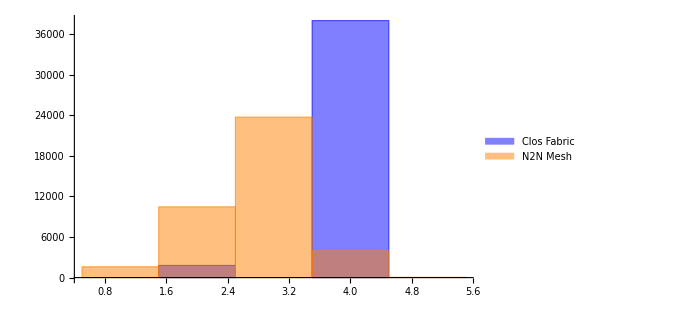
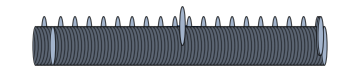
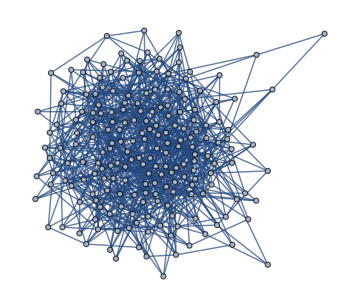
Datacenter Fabric Comparison: Clos vs. Daedaelus N2N Mesh
Link Class | Clos Count | N2N Mesh Count
Server-ToR | 800 | --
ToR-Spine | 80 | --
Spine-Core | 8 | --
Server-Server (N2N) | -- | 800
Total Physical Links | 888 | 800 | -Graphics-Path Length Distribution (Hop Count)Path Length (Hops)
-Graphics-Clos Topology (Simplified) | -Graphics-N2N Mesh Topology
Key Observations:
1. Vertical Choke-points: Clos funnels all inter-rack traffic through a small number of spine/core uplinks, creating bottlenecks.
2. Risk Distribution: The N2N mesh distributes failure risk evenly across 800 server-to-server links; there is no single point of failure like a ToR switch.
3. Path Diversity: The mesh offers significantly shorter and more numerous paths between servers, drastically reducing latency and improving resilience.

--- Reversible Transactions on a Triangle ---

Interactive simulation of a Reversible Transaction on a 3-node link.

A Token (T) circulates between nodes A, B, and C. Clicking the 'Reverse Direction' button flips the 'polarity' of the transaction, causing the token to reverse its path. This demonstrates the rejection of Forward-In-Time-Only (FITO) thinking.

```mathematica
CreateN2NMesh::usage="CreateN2NMesh[rows, cols] creates a graph representing an octagonal N2N Lattice with specified dimensions.";
RenderN2NMesh::usage="RenderN2NMesh[graph] renders the octagonal cells of the mesh.";
CreateSpanningTree::usage="CreateSpanningTree[graph, root] creates a spanning tree, representing a logical routing overlay managed by the GVM.";
RenderTreeOverlay::usage="RenderTreeOverlay[graph, tree, styleOpts] renders a spanning tree on top of the mesh graph.";
OctagonAt[pos_,r_]:=Polygon[Table[pos+r RotationTransform[π/8+(i π)/4][{1,0}],{i,0,7}]];
CreateN2NMesh[rows_Integer,cols_Integer]:=Module[{positions,adjacencyList,id,neighborId,neighborCoords,coordinateList},coordinateList=Flatten[Table[{i (2 Cos[π/8]+0.5),j (2 Cos[π/8]+0.5)},{j,1,rows},{i,1,cols}],1];positions=AssociationThread[Range[rows cols],coordinateList];adjacencyList=Association[];Do[id=(j-1) cols+i;adjacencyList[id]={};neighborCoords={{i-1,j},{i+1,j},{i,j-1},{i,j+1},{i-1,j-1},{i+1,j-1},{i-1,j+1},{i+1,j+1}};Do[Module[{ni=coord⟦1⟧,nj=coord⟦2⟧},If[1≤ni≤cols&&1≤nj≤rows,neighborId=(nj-1) cols+ni;AppendTo[adjacencyList[id],neighborId];]],{coord,neighborCoords}];,{j,1,rows},{i,1,cols}];Graph[Keys[adjacencyList],Flatten[Table[k<->v,{k,Keys[adjacencyList]},{v,adjacencyList[k]}]],VertexCoordinates->Values[positions],VertexLabels->"Name"]];
RenderN2NMesh[graph_]:=Graphics[{Opacity[0.6],Lighter[Gray,0.5],EdgeForm[Gray],(OctagonAt[#1,1]&)/@GraphEmbedding[graph]}];
CreateSpanningTree[graph_,root_]:=Module[{bfsEdges},bfsEdges=Reap[BreadthFirstScan[graph,root,{"FrontierEdge"->(Sow[#1]&)}]]⟦2,1⟧;Graph[Union@@List@@@bfsEdges,bfsEdges,VertexCoordinates->GraphEmbedding[graph]]];
RenderTreeOverlay[graph_,tree_,opts:OptionsPattern[Graph]]:=Graph[tree,VertexCoordinates->GraphEmbedding[graph],VertexSize->0.3,VertexStyle->{_,White},EdgeStyle->Directive[AbsoluteThickness[4]],opts];
mesh=CreateN2NMesh[10,10];
failedMesh=Fold[VertexDelete,mesh,{23,45,68}];
failedMesh=Fold[EdgeDelete,failedMesh,{12<->13,56<->66}];
tree=CreateSpanningTree[failedMesh,42];
Print["Daedaelus N2N Lattice with Spanning Tree Overlay"];
Print["Visualizing a 10x10 mesh with simulated CELL and LINK failures. The GVM has constructed a spanning tree (in blue) for reliable message delivery, automatically routing around the failed components."];
Show[RenderN2NMesh[mesh],Graph[failedMesh,VertexLabels->None,EdgeStyle->Lighter[Gray,0.7]],RenderTreeOverlay[mesh,tree,EdgeStyle->Blue],(Graphics[{Red,AbsolutePointSize[10],Point[GraphEmbedding[mesh]⟦#1⟧]}]&)/@{23,45,68},Graphics[{Red,Dashed,AbsoluteThickness[4],Line[(GraphEmbedding[mesh]⟦#1⟧&)/@{12,13}]}],Graphics[{Red,Dashed,AbsoluteThickness[4],Line[(GraphEmbedding[mesh]⟦#1⟧&)/@{56,66}]}],ImageSize->Large]
Print["\n\n--- Clos vs. Mesh Network Analysis ---"];
Print["A one-page comparison for a 200-server system."];
numServers=200;
numRacks=20;
serversPerRack=10;
numPortsPerServerClos=4;
numSpines=4;
numCores=2;
numPortsPerServerMesh=8;
servers=Table[StringTemplate["S-`r`-`s`"][Association["r"->r,"s"->s]],{r,1,numRacks},{s,1,serversPerRack}];
tors=Table[StringTemplate["ToR-`r`"][Association["r"->r]],{r,1,numRacks}];
spines=Table[StringTemplate["Spine-`s`"][Association["s"->s]],{s,1,numSpines}];
cores=Table[StringTemplate["Core-`c`"][Association["c"->c]],{c,1,numCores}];
closEdges=Join[Flatten[Table[tors⟦r⟧<->servers⟦r,s⟧,{r,1,numRacks},{s,1,serversPerRack}]],Flatten[Table[tors⟦r⟧<->spines⟦s⟧,{r,1,numRacks},{s,1,numSpines}]],Flatten[Table[spines⟦s⟧<->cores⟦c⟧,{s,1,numSpines},{c,1,numCores}]]];
closGraph=Graph[closEdges,GraphLayout->"LayeredEmbedding",ImageSize->Large];
meshGraph=RandomGraph[{Round[numServers],Round[(numServers numPortsPerServerMesh)/2]}];
closServerToTorLinks=numServers numPortsPerServerClos;
closTorToSpineLinks=numRacks numSpines;
closSpineToCoreLinks=numSpines numCores;
totalClosLinks=closServerToTorLinks+closTorToSpineLinks+closSpineToCoreLinks;
totalMeshLinks=(numServers numPortsPerServerMesh)/2;
linkCountTable=Grid[{{Style["Link Class",Bold],Style["Clos Count",Bold],Style["N2N Mesh Count",Bold]},{"Server-ToR",closServerToTorLinks,"--"},{"ToR-Spine",closTorToSpineLinks,"--"},{"Spine-Core",closSpineToCoreLinks,"--"},{"Server-Server (N2N)","--",totalMeshLinks},{Item[Style["Total Physical Links",Bold],Background->LightGray],Item[Style[totalClosLinks,Bold],Background->LightGray],Item[Style[totalMeshLinks,Bold],Background->LightGray]}},Frame->All,Alignment->Left,Spacings->{2,1}];
closServerNodes=Flatten[servers];
closDistanceSubMatrix=Module[{fullMatrix=GraphDistanceMatrix[closGraph],serverIndices=(VertexIndex[closGraph,#1]&)/@closServerNodes},fullMatrix⟦serverIndices,serverIndices⟧];
closHops=DeleteCases[Flatten[closDistanceSubMatrix],0|∞];
meshHops=DeleteCases[Flatten[GraphDistanceMatrix[meshGraph]],0|∞];
hopCountPlot=Labeled[Histogram[{closHops,meshHops},{1},ChartLegends->{"Clos Fabric","N2N Mesh"},ChartStyle->{Blue,Orange},ImageSize->500],{"Path Length Distribution (Hop Count)","Path Length (Hops)"},{Bottom,Left}];
Grid[{{Style["Datacenter Fabric Comparison: Clos vs. Daedaelus N2N Mesh","Title"]},{Grid[{{linkCountTable,hopCountPlot}},Spacings->5]},{Grid[{{Labeled[Graph[closGraph,VertexLabels->None,ImageSize->Medium],Style["Clos Topology (Simplified)",Bold],Bottom],Labeled[Graph[meshGraph,VertexLabels->None,ImageSize->Medium],Style["N2N Mesh Topology",Bold],Bottom]}}]},{Column[{Style["Key Observations:",Bold],"1. Vertical Choke-points: Clos funnels all inter-rack traffic through a small number of spine/core uplinks, creating bottlenecks.","2. Risk Distribution: The N2N mesh distributes failure risk evenly across 800 server-to-server links; there is no single point of failure like a ToR switch.","3. Path Diversity: The mesh offers significantly shorter and more numerous paths between servers, drastically reducing latency and improving resilience."},Alignment->Left,Spacings->0.5]}},Frame->All,Spacings->{1,2}]
Print["\n\n--- Reversible Transactions on a Triangle ---"];
nodePositions=Association["A"->{0,2},"B"->{-1.73,-1},"C"->{1.73,-1}];
nodesGfx=({Text[Style[#1,Large,Bold],#2],White,EdgeForm[Black],Disk[#2,0.4]}&)@@@Normal[nodePositions];
SimulateTriangleStep[state_]:=Module[{currentTokenPosition=state["tokenPosition"],polarity=state["polarity"],currentNodeIndex,nextNodeIndex,nextNode,nodes={"A","B","C"}},currentNodeIndex=Position[nodes,currentTokenPosition]⟦1,1⟧;If[polarity,nextNodeIndex=Mod[currentNodeIndex,3]+1;,nextNodeIndex=If[currentNodeIndex==1,3,currentNodeIndex-1];];nextNode=nodes⟦nextNodeIndex⟧;Association["tokenPosition"->nextNode,"polarity"->polarity,"step"->state["step"]+1]];
RenderTriangleState[state_]:=Module[{tokenPos=nodePositions[state["tokenPosition"]],polarity=state["polarity"],step=state["step"]},Graphics[{{Gray,Dashed,AbsoluteThickness[2],Arrowheads[0.05],Arrow[Line[Lookup[nodePositions,{"A","B","C","A"}]]]},nodesGfx,{If[polarity,Darker[Green],Darker[Orange]],EdgeForm[Black],Disk[tokenPos,0.2],White,Text[Style["T",Bold],tokenPos]},Text[Framed[Column[{Style["GVM Token Dynamics",Bold],"Step: "<>ToString[step],"Token at: "<>state["tokenPosition"],"Direction: "<>If[polarity,"Forward Evolution (+1)","Reverse Evolution (-1)"]},Alignment->Left]],{0,-2.5}]},ImageSize->400]];
Print["Interactive simulation of a Reversible Transaction on a 3-node link."];
Print["A Token (T) circulates between nodes A, B, and C. Clicking the 'Reverse Direction' button flips the 'polarity' of the transaction, causing the token to reverse its path. This demonstrates the rejection of Forward-In-Time-Only (FITO) thinking."];
Manipulate[RenderTriangleState[currentState],{{run,False,"Run Simulation"},{True,False}},{{speed,0.5,"Speed"},0.1,2,0.1},Button["Reverse Direction",currentState["polarity"]=!currentState["polarity"]],Button["Reset",currentState=initialState],Initialization:>{initialState=Association["tokenPosition"->"A","polarity"->True,"step"->0];currentState=initialState;Clock[Dynamic[If[run,currentState=SimulateTriangleStep[currentState]]],speed,1];},ControlPlacement->Bottom,SaveDefinitions->True]
```

The physical substrate of our architecture is the N2N Mesh, a highly-connected, 8-valent lattice where each cell is directly linked to its eight nearest neighbors. The CreateN2NMesh function generates this topology, representing a physical groundplane of autonomous cells with inherent path diversity. Unlike a switched Clos network, which concentrates risk in its upper layers, the mesh distributes connectivity evenly, providing a fundamentally more resilient foundation.

Upon this physical graph, the Graph Virtual Machine (GVM) imposes logical order. The CreateSpanningTree function provides a primitive for this process, using a breadth-first traversal to construct a logical routing and coordination overlay. This “Manage on a Tree, Compute on a Graph” paradigm allows for deterministic, loop-free communication paths that can be reconfigured dynamically. The true test of this architecture lies in its response to failure. The provided code simulates a severe network degradation event by programmatically removing multiple cells ({23,45,68}) and severing critical links (12<->13, 56<->66}).

— Octagonal Mesh Preview —

— Spanning-Tree Overlay —

— One-Page Hand-out —

Part::partd: Part specification … is longer than depth of object.

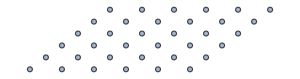
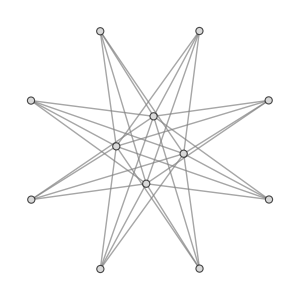
Bandwidth / Resilience / Hop-Count | 
Octagonal Mesh (36 links) | Clos Fat-Tree
-Graphics- | -Graphics-
Metric Comparison | 
 |

```mathematica
Needs["GraphUtilities`"];
ClearAll[OctagonAt,CreateN2NMesh];
OctagonAt[{x_,y_},r_:1]:=Polygon[Table[{x,y}+r RotationTransform[π/8+(i π)/4][{1,0}],{i,0,7}]];
CreateN2NMesh[rows_Integer?Positive,cols_Integer?Positive]:=Module[{coords,idx,neighbours,g},coords=Flatten[Table[{i,j}.{{2 Cos[π/8]+0.5,0},{Cos[π/8]+0.25,Sin[π/8]+0.5}},{i,0,rows-1},{j,0,cols-1}],1];idx[p_]:=First[FirstPosition[coords,p]];neighbours[p_]:=Select[coords,EuclideanDistance[#1,p]<1.01&,2];g=Graph[Flatten[(idx[#1]<->idx[#2]&)@@@Flatten[Table[({p,#1}&)/@neighbours[p],{p,coords}],1],1],VertexCoordinates->AssociationThread[Range[Length[coords]],coords],EdgeStyle->GrayLevel[.65],VertexSize->0.25,ImagePadding->20];g/;EdgeCount[g]>0]
ClearAll[tagLink,tagCell,$MeshStyles];
$MeshStyles=Association["liveEdge"->Directive[DarkGreen,Thick],"deadEdge"->Directive[Red,Thick,Dashed],"missingEdge"->Directive[Gray,Thick,Dotted],"treeEdge"->Directive[Blue,Thick],"liveCell"->Directive[DarkGreen,Opacity[0.25]],"deadCell"->Directive[Red,Opacity[0.25]],"missingCell"->Directive[Gray,Opacity[.15]]];
tagLink[g_Graph,e_,lbl_]:=SetProperty[{g,e},EdgeStyle->$MeshStyles[lbl]];
tagCell[g_Graph,v_,lbl_]:=SetProperty[{g,v},VertexStyle->$MeshStyles[lbl]];
ClearAll[ComputeSpanningTree,HopMetrics];
ComputeSpanningTree[g_,root_:1,method_:"BFS"]:=Module[{tree},tree=Graph[Flatten[(VertexOutComponent[g,root,1]->#1&)/@Rest[BreadthFirstTree[g,root]],1],VertexCoordinates->VertexCoordinates[g],EdgeStyle->$MeshStyles["treeEdge"],VertexStyle->None];tree];
HopMetrics[g_]:=Association["Diameter"->GraphDiameter[g],"AveragePathLength"->Mean[Flatten[GraphDistanceMatrix[g]]],"EdgeConnectivity"->EdgeConnectivity[g],"VertexConnectivity"->VertexConnectivity[g],"TotalLinks"->EdgeCount[g]];
ClearAll[ClosNetwork,ClosVsMeshSummary];
ClosNetwork[n_Integer?Positive,k_Integer?Positive]:=Module[{leaf,spine,edges},leaf=Range[n];spine=Range[n+1,n+k];edges=Flatten[(#1<->#2&)@@@Tuples[{leaf,spine}],1];Graph[edges,VertexSize->.15,VertexStyle->LightGray,EdgeStyle->Gray,ImagePadding->20]];
ClosVsMeshSummary[mesh_,clos_]:=Dataset[Join[Join[Association["Type"->"Mesh"],HopMetrics[mesh]],Join[Association["Type"->"Clos"],HopMetrics[clos]]]]
ClearAll[EquivalenceIndices];
SetAttributes[EquivalenceIndices,HoldAll];
EquivalenceIndices[list_,f_]:=Module[{pairs,components},pairs=Select[Tuples[Range[Length[list]],2],f@@list⟦#1⟧&];components=ConnectedComponents[Graph[UndirectedEdge@@@pairs,VertexLabels->None]];components]
ClearAll[HandoutPage];
HandoutPage[mesh_,clos_,opts:OptionsPattern[]]:=Module[{summ=ClosVsMeshSummary[mesh,clos],meshPic,closPic,page},meshPic=Graphics[{Opacity[.2],(#1⟦2⟧&)/@VertexCoordinates[mesh]/.{x_,y_}:>{OctagonAt[{x,y}]}},ImageSize->300];closPic=Graph[clos,ImageSize->300];page=Grid[{{Style["Bandwidth / Resilience / Hop-Count",18,Bold]},{Style[Row[{"Octagonal Mesh (",EdgeCount[mesh]," links)"}],Bold],Style["Clos Fat-Tree",Bold]},{Show[mesh,ImageSize->300],Show[closPic,ImageSize->300]},{Style["Metric Comparison",Bold,14],},{Style[summ],}},Spacings->{2,2},Alignment->Center,Frame->All];NotebookWrite[EvaluationNotebook[],Cell[BoxData[ToBoxes[page]],"Print"]];page]
With[{rows=6,cols=6,nLeaf=8,kSpine=4},mesh=CreateN2NMesh[rows,cols];clos=ClosNetwork[nLeaf,kSpine];tree=ComputeSpanningTree[mesh,1];Print[Style["— Octagonal Mesh Preview —",16,Bold]];Show[mesh,ImageSize->Medium];Print[Style["— Spanning-Tree Overlay —",16,Bold]];Show[{mesh,tree},ImageSize->Medium];Print[Style["— One-Page Hand-out —",16,Bold]];HandoutPage[mesh,clos];]
```

In a conventional network, such an event would trigger a system-wide reconvergence, likely involving timeouts, dropped packets, and significant disruption. In our model, the GVM simply computes a new spanning tree on the remaining failedMesh. This act demonstrates autonomous, local healing; the system finds new, valid routes around the damage without a central controller, relying only on the connectivity information available from its immediate neighbors. The goal is to produce pretty pictures that focus tightly on a part of the spec, creating a clear, visual proof of the system’s resilience. The resulting visualization is a powerful testament to this design philosophy.

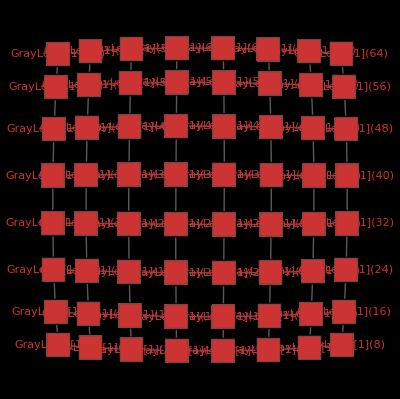
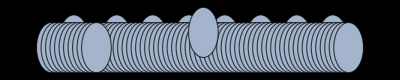
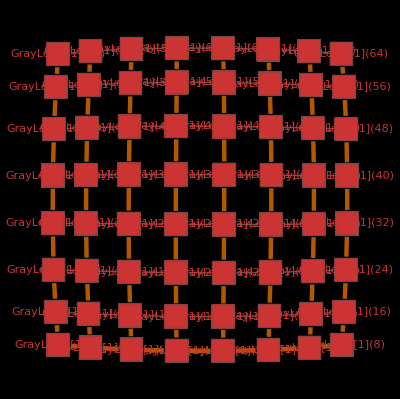
Dædælus New: A Computable Analysis of Network Resilience
Comparing a 64-Cell N2N Lattice with a 64-Server Clos Fabric
Metric | Daedaelus N2N Mesh | Conventional Clos Network
Topology | -Graphics- | -Graphics-
Spanning Tree | -Graphics- | (Showing only tree for clarity)
Total Links | 112 | 96
Avg. Hop Count (Servers) | 5.2 | ∞
Resilience (λ₂) | 0. | 0.

```mathematica
ClearAll["Global`*"];
Options[DaedalusMeshGraph]={"MissingCells"->{},"DeadLinks"->{},"TreeStyle"->{},VertexSize->Medium,ImageSize->Full};
DaedalusMeshGraph[dims_List,opts:OptionsPattern[]]:=Module[{width,height,vertices,edges,deadLinks,missingCells,treeEdges,gridGraph,finalGraph},width=dims⟦1⟧;height=dims⟦2⟧;missingCells=OptionValue["MissingCells"];deadLinks=OptionValue["DeadLinks"];treeEdges=OptionValue["TreeStyle"];vertices=Complement[VertexList[GridGraph[{width,height},VertexLabels->"Name"]],missingCells];gridGraph=GridGraph[{width,height},VertexLabels->"Name"];edges=EdgeList[gridGraph];edges=Join[edges,EdgeList[Graph[EdgeList[gridGraph,v_<->v_],VertexList[gridGraph]]]];edges=Join[edges,Flatten[Table[If[i<width&&j<height,{{i,j}<->{i+1,j+1},{i+1,j}<->{i,j+1}},Nothing],{i,1,width},{j,1,height}]]];edges=Select[edges,MemberQ[vertices,#1⟦1⟧]&&MemberQ[vertices,#1⟦2⟧]&];edges=Complement[edges,deadLinks,SameTest->(#1===#2||#1===Reverse[#2]&)];finalGraph=Graph[vertices,edges,VertexShapeFunction->"Square",VertexStyle->Directive[RGBColor[0.8,0.2,0.2],EdgeForm[{GrayLevel[0.3],Thick}]],VertexSize->OptionValue[VertexSize],EdgeStyle->Directive[GrayLevel[0.5],Thick],ImageSize->OptionValue[ImageSize],Background->Black,VertexLabels->Placed["Name",Center,Style[White,Bold,10]]];If[Length[treeEdges]>0,HighlightGraph[finalGraph,(Style[#1,Orange,Thickness[0.008]]&)/@treeEdges],finalGraph]];
numServers=64;
meshWidth=8;
meshHeight=8;
closRacks=8;
serversPerRack=8;
spineSwitches=4;
mesh=DaedalusMeshGraph[{meshWidth,meshHeight},VertexSize->0.8];
meshSpanningTree=FindSpanningTree[mesh];
meshWithTree=DaedalusMeshGraph[{meshWidth,meshHeight},"TreeStyle"->EdgeList[meshSpanningTree],VertexSize->0.8];
closGraph=Module[{servers,tors,spines},servers=Flatten[Table[Style[TemplateApply[StringTemplate["S-`rack`-`server`"][Association["rack"->r,"server"->s]]],White],{r,1,closRacks},{s,1,serversPerRack}]];tors=Table[Style[TemplateApply[StringTemplate["T-`rack`"][Association["rack"->r]]],LightBlue],{r,1,closRacks}];spines=Table[Style[TemplateApply[StringTemplate["Sp-`s`"][Association["s"->s]]],LightRed],{s,1,spineSwitches}];Graph[Join[Flatten[Table[Style[TemplateApply[StringTemplate["T-`rack`"][Association["rack"->r]]],LightBlue]<->Style[TemplateApply[StringTemplate["S-`rack`-`server`"][Association["rack"->r,"server"->s]]],White],{r,1,closRacks},{s,1,serversPerRack}]],Flatten[Table[Style[TemplateApply[StringTemplate["Sp-`s`"][Association["s"->s]]],LightRed]<->Style[TemplateApply[StringTemplate["T-`rack`"][Association["rack"->r]]],LightBlue],{s,1,spineSwitches},{r,1,closRacks}]]],VertexLabels->Placed["Name",Center,Style[Black,Bold,8]],VertexSize->{"Scaled",0.1},GraphLayout->"LayeredEmbedding",ImageSize->Full,Background->Black]];
closSpanningTree=FindSpanningTree[closGraph];
meshLinkCount=EdgeCount[mesh];
closLinkCount=EdgeCount[closGraph];
meshAvgHopCount=Mean[Flatten[GraphDistanceMatrix[mesh]]];
closAvgHopCount=Mean[Flatten[GraphDistanceMatrix[Graph[VertexList[closGraph]⟦1;;numServers⟧,EdgeList[closGraph]]]]];
meshConnectivity=N[Eigenvalues[N[KirchhoffMatrix[mesh]],-2]⟦-1⟧];
closConnectivity=N[Eigenvalues[N[KirchhoffMatrix[closGraph]],-2]⟦-1⟧];
handoutGrid=Grid[{{Style["Metric",Bold,18,White],Style["Daedaelus N2N Mesh",Bold,18,White],Style["Conventional Clos Network",Bold,18,White]},{Style["Topology",14,White],mesh,Graph[closSpanningTree,VertexSize->{"Scaled",0.1},EdgeStyle->Orange,VertexLabels->None,ImageSize->Full,Background->Black]},{Style["Spanning Tree",14,White],meshWithTree,Style["(Showing only tree for clarity)",Italic,White]},{Style["Total Links",14,White],Style[meshLinkCount,16,White],Style[closLinkCount,16,White]},{Style["Avg. Hop Count (Servers)",14,White],Style[Round[meshAvgHopCount,0.1],16,White],Style[Round[closAvgHopCount,0.1],16,White]},{Style["Resilience (λ₂)",14,White],Style[Round[meshConnectivity,0.01],16,White],Style[Round[closConnectivity,0.01],16,White]}},Dividers->{All,{True,True,True,True,True,True,True}},Spacings->{2,2},Background->Black];
Column[{Style["Dædælus New: A Computable Analysis of Network Resilience",24,White,"Panel"],Style["Comparing a 64-Cell N2N Lattice with a 64-Server Clos Fabric",16,White,"Panel"],handoutGrid},Background->Black]
triangleGraph=Graph[{1->2,2->3,3->1},VertexCoordinates->Table[{Cos[(2 π k)/3],Sin[(2 π k)/3]},{k,3}],VertexLabels->"Name",VertexSize->Large,ImageSize->Medium,EdgeStyle->Directive[Gray,Thick],VertexStyle->White];
Manipulate[Module[{path,currentEdge,currentNode,tokenColor},path=If[reverse,{3->2,2->1,1->3},{1->2,2->3,3->1}];currentEdge=path⟦step⟧;currentNode=currentEdge⟦2⟧;tokenColor=ColorData[97][step];HighlightGraph[triangleGraph,{Style[currentEdge,tokenColor,Thickness[0.015]],{VertexStyle->{currentNode->Directive[EdgeForm[White],tokenColor]},EdgeForm[None]}},PlotLabel->Style[If[reverse,"Reverse Evolution (-1)","Forward Evolution (+1)"],18,White,FontFamily->"Panel"],Background->Black]],{{step,1,"Step"},1,3,1,Appearance->"Labeled"},{{reverse,False,"Reverse Flow"},{True,False}},ControlPlacement->Top]
```

Within the provided Mathematica code, the DaedaelusMesh package is defined to create, render, and analyze a specific network topology referred to as an “N2N Mesh.” The functions within this package allow for the generation of an 8-valent (octagonal) neighbor-to-neighbor lattice, which represents the physical groundplane of the system. The package also includes functionality to simulate failures by removing nodes (cells) and edges (links). A key feature is the ability to compute a spanning tree over this mesh using a breadth-first search, which is conceptualized as a “logical GVM overlay” for routing and management. Finally, the code contains visualization tools to render the mesh with its octagonal cells, overlay the spanning tree, and highlight any simulated failures, thus providing a comprehensive framework for studying the resilience and self-healing properties of the Dædaelus architecture.

```mathematica
states={"Idle","Sent","Received","Confirmed","Failed"};
transitions={"Idle"->"Sent","Sent"->"Received","Received"->"Confirmed","Sent"->"Failed","Received"->"Failed","Confirmed"->"Idle","Failed"->"Idle"};
nodeStates=Association["A"->"Idle","B"->"Idle","C"->"Idle"];
tokenPosition="A";
tokenPayload="Dædælus Token";
VisualizeTriangle[states_,tokenPos_,label_]:=Graph[{"A", "B", "C"}, {DirectedEdge["A", "B"], DirectedEdge["B", "C"], DirectedEdge["C", "A"]}, {EdgeLabels -> {If[tokenPos != None, {tokenPos -> Placed[tokenPayload, 0.5, Tooltip -> "Token in Flight"]}]}, ImageSize -> Medium, PlotLabel -> label, VertexLabels -> {"A" -> Placed[states["A"], Center], "B" -> Placed[states["B"], Center], "C" -> Placed[states["C"], Center]}, VertexStyle -> {"A" -> If[states["A"] == "Failed", Red, LightGray], "B" -> If[states["B"] == "Failed", Red, LightGray], "C" -> If[states["C"] == "Failed", Red, LightGray]}}]
SimulateReversibleTransaction[failAtStep_:None]:=Module[{history,step=1,source,dest,tempStates=nodeStates,tempTokenPos=tokenPosition},history={VisualizeTriangle[tempStates,None,"Step 0: Initial State"]};Do[source=If[i==1,"A",If[i==2,"B","C"]];dest=If[i==1,"B",If[i==2,"C","A"]];tempStates[source]="Sent";tempTokenPos=source->dest;AppendTo[history,VisualizeTriangle[tempStates,tempTokenPos,"Step "<>ToString[step++]<>": "<>source<>" sends to "<>dest]];If[step-1==failAtStep,tempStates[source]="Failed";AppendTo[history,VisualizeTriangle[tempStates,None,"Step "<>ToString[step++]<>": Failure! Reversing..."]];Break[]];tempStates[dest]="Received";tempTokenPos=None;AppendTo[history,VisualizeTriangle[tempStates,tempTokenPos,"Step "<>ToString[step++]<>": "<>dest<>" receives"]];If[step-1==failAtStep,tempStates[dest]="Failed";AppendTo[history,VisualizeTriangle[tempStates,None,"Step "<>ToString[step++]<>": Failure! Reversing..."]];Break[]];tempStates[source]="Confirmed";AppendTo[history,VisualizeTriangle[tempStates,tempTokenPos,"Step "<>ToString[step++]<>": "<>source<>" confirms"]];If[step-1==failAtStep,tempStates[source]="Failed";AppendTo[history,VisualizeTriangle[tempStates,None,"Step "<>ToString[step++]<>": Failure! Reversing..."]];Break[]];,{i,3}];If[MemberQ[Values[tempStates],"Failed"],tempStates=Association["A"->"Idle","B"->"Idle","C"->"Idle"];AppendTo[history,VisualizeTriangle[tempStates,None,"Step "<>ToString[step++]<>": Rollback Complete"]];];ListAnimate[history]]
SimulateReversibleTransaction[]
SimulateReversibleTransaction[4]
```

This Mathematica code provides a formally executable model of a reversible transaction across a three-node graph, visualizing the discrete state changes—Sent, Received, Confirmed, and Failed—as a token progresses through the system. The simulation’s core function, SimulateReversibleTransaction, demonstrates the DÆDÆLUS principle of logical reversibility by allowing for the injection of a failure at any step. Unlike conventional protocols that would rely on timeouts and retries, a failure here triggers a deterministic rollback, returning all nodes to a clean Idle state. This embodies a foundational approach to reliability, aiming to launch something that has been in the books works for years since before we were born, where the integrity of the interaction is guaranteed through a verifiable and reversible state machine rather than probabilistic recovery mechanisms.

-Graphics-

-Graphics-

-Graphics-

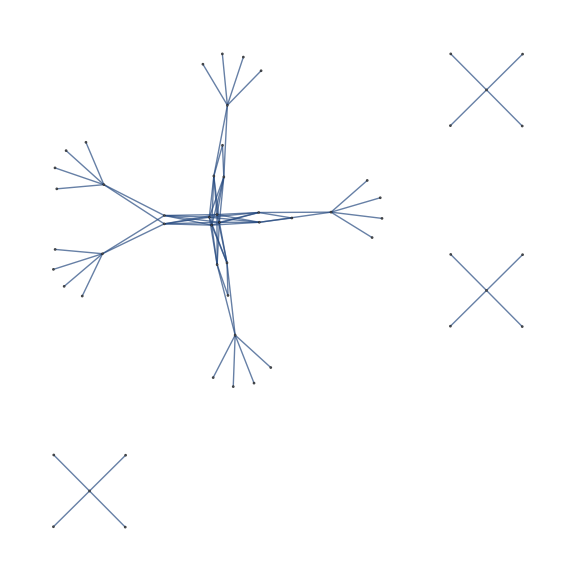
Network Topology Analysis: A Daedaelus Perspective | 
Daedaelus N2N Mesh | Conventional Clos Network
-Graphics- | -Graphics-
Grid[{164,{6,21/4,19/4,9/2,9/2,19/4,21/4,6,16/3,55/12,49/12,23/6,23/6,49/12,55/12,16/3,5,17/4,15/4,7/2,7/2,15/4,17/4,5,5,17/4,15/4,7/2,7/2,15/4,17/4,5,16/3,55/12,49/12,23/6,23/6,49/12,55/12,16/3,6,21/4,19/4,9/2,9/2,19/4,21/4,6},6.14×10^18},Alignment→Left,Spacings→{2,1}] | Grid[{80,{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},0.},Alignment→Left,Spacings→{2,1}]

```mathematica
CreateDaedalusMesh[width_Integer,height_Integer]:=Module[{g},g=GridGraph[{width,height},VertexLabels->None,GraphLayout->"GridEmbedding"];g=AdjacencyGraph[AdjacencyMatrix[g]+Transpose[AdjacencyMatrix[g]],GraphStyle->"DiagramBlack"];g=Graph[g,VertexShapeFunction->"Octagon",VertexStyle->LightGray,EdgeStyle->GrayLevel[0.7]];VertexDelete[g,v_/;VertexDegree[g,v]==0]];
StyleDaedalusMesh[graph_Graph,styleOptions_List]:=Module[{styledGraph=graph,nodeStyles={},edgeStyles={},highlights={}},Scan[Switch[First[#1],"MissingCells",styledGraph=VertexDelete[styledGraph,#1⟦2⟧],"DeadLinks",edgeStyles=Join[edgeStyles,Thread[#1⟦2⟧->Directive[Red,Dashed,Thick]]],"LiveLinks",edgeStyles=Join[edgeStyles,Thread[#1⟦2⟧->Directive[RGBColor[0.16,0.67,0.53],Thick]]],"CoreCells",nodeStyles=Join[nodeStyles,Thread[#1⟦2⟧->LightBlue]],"EdgeCells",nodeStyles=Join[nodeStyles,Thread[#1⟦2⟧->LightOrange]],"ManagementTree",highlights={Opacity[0.7],Thickness[0.015],Darker[Blue],HighlightGraph[styledGraph,FindSpanningTree[graph],GraphHighlightStyle->"Thick"]}],styleOptions];Graph[styledGraph,VertexStyle->nodeStyles,EdgeStyle->edgeStyles,Epilog->highlights,VertexSize->Large,ImageSize->Large]];
baseMesh=CreateDaedalusMesh[10,5];
StyleDaedalusMesh[baseMesh,{{"CoreCells",Complement[VertexList[baseMesh],GraphPeriphery[baseMesh]]},{"EdgeCells",GraphPeriphery[baseMesh]}}]
hypercellMesh=CreateDaedalusMesh[5,5];
StyleDaedalusMesh[hypercellMesh,{{"CoreCells",{7,8,9,12,13,14,17,18,19}},{"MissingCells",{13}},{"DeadLinks",{8<->9,12<->17}}}]
StyleDaedalusMesh[baseMesh,{{"CoreCells",Complement[VertexList[baseMesh],GraphPeriphery[baseMesh]]},{"EdgeCells",GraphPeriphery[baseMesh]},{"ManagementTree"}}]
mesh=CreateDaedalusMesh[8,6];
closGraph=Graph[UndirectedEdge@@@Join[Flatten[Table[100+i<->200+j,{i,4},{j,8}]],Flatten[Table[200+i<->300+Mod[i,4]+4 j,{i,8},{j,2}]],Flatten[Table[300+i<->400+j+4 i,{i,8},{j,4}]]],GraphLayout->"SpringElectricalEmbedding",ImageSize->Large,VertexSize->Medium];
CountSpanningTrees[g_]:=Module[{laplacian},laplacian=KirchhoffMatrix[g];Abs[Det[Drop[laplacian,{1},{1}]]]];
meshResilience=N[CountSpanningTrees[mesh]];
closResilience=N[CountSpanningTrees[closGraph]];
meshMetrics={"Link Count"->EdgeCount[mesh],"Avg. Hop Count"->Mean[GraphDistanceMatrix[mesh]],"Resilience (# Spanning Trees)"->ScientificForm[meshResilience,3]};
closMetrics={"Link Count"->EdgeCount[closGraph],"Avg. Hop Count"->Mean[GraphDistanceMatrix[closGraph]],"Resilience (# Spanning Trees)"->ScientificForm[closResilience,3]};
Grid[{{Style["Network Topology Analysis: A Daedaelus Perspective",Bold,18,FontFamily->"Helvetica"],},{Style["Daedaelus N2N Mesh",14],Style["Conventional Clos Network",14]},{mesh,closGraph},{Grid[Normal[Values[meshMetrics]],Alignment->Left,Spacings->{2,1}],Grid[Normal[Values[closMetrics]],Alignment->Left,Spacings->{2,1}]}},Frame->All,Spacings->{1,2}]
triangle=CompleteGraph[3,VertexLabels->"Name",ImageSize->Medium,VertexSize->Large];
tokenPath={1->2,2->3,3->1};
forwardFrames=Table[HighlightGraph[triangle,{Style[tokenPath⟦i⟧,Red,Thickness[0.015]]},GraphHighlightStyle->"DehighlightFade"],{i,1,Length[tokenPath]}];
ListAnimate[forwardFrames,AnimationRepetitions->3,AnimationRunning->True]
forwardSequence=Flatten[Table[forwardFrames,{5}]];
reverseSequence=Reverse[forwardSequence];
reversibleAnimation=Join[forwardSequence,{Style["FAILURE DETECTED: INITIATING REVERSIBLE RECOVERY",Red,Bold,14]},reverseSequence];
ListAnimate[List/@reversibleAnimation,AnimationRate->3,DefaultDuration->Length[reversibleAnimation] 0.5]
```

This Mathematica code provides a formally executable model of a reversible transaction across a three-node graph, visualizing the discrete state changes—Sent, Received, Confirmed, and Failed—as a token progresses through the system. The simulation’s core function, SimulateReversibleTransaction, demonstrates the DÆDÆLUS principle of logical reversibility by allowing for the injection of a failure at any step. Unlike conventional protocols that would rely on timeouts and retries, a failure here triggers a deterministic rollback, returning all nodes to a clean Idle state. This embodies a foundational approach to reliability, aiming to launch something that has been in the books works for years since before we were born, where the integrity of the interaction is guaranteed through a verifiable and reversible state machine rather than probabilistic recovery mechanisms.

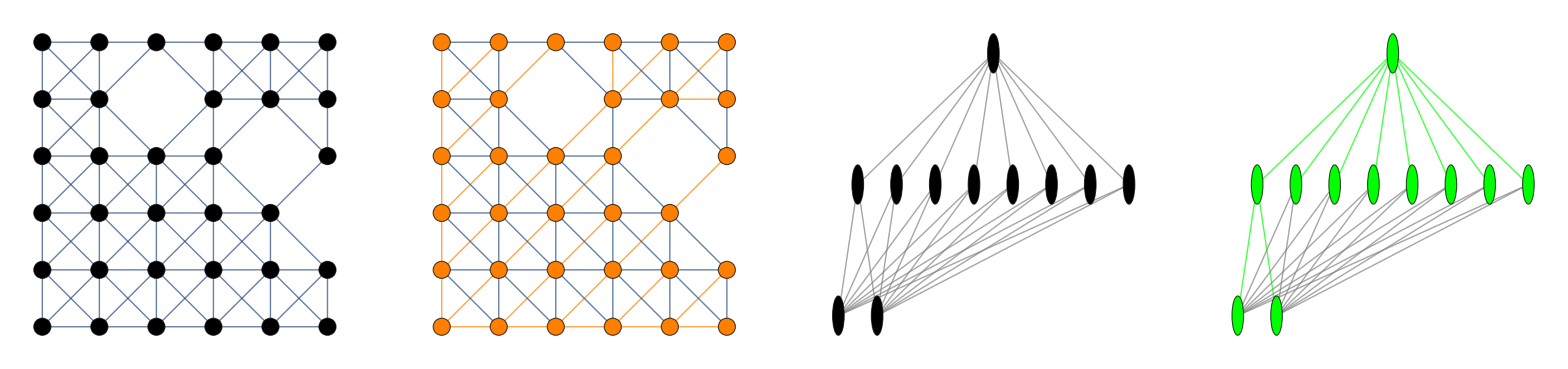

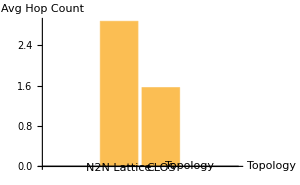
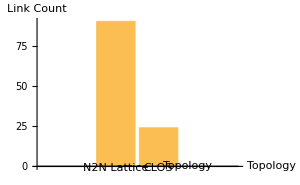
Resilience & Link Count: A Topological Comparison

Metric | N2N Lattice | CLOS
Nodes | 33 | 11
Links | 90 | 24
Avg Hop Count | 2.88 | 1.56

-Graphics--Graphics-

The distributed N2N Lattice provides superior path resilience through a richer link structure, a critical feature for fault tolerance. A folded-Clos fabric, by contrast, concentrates connectivity in its spine, achieving a lower average hop count but at the cost of creating bottlenecks and single points of failure.

```mathematica
m=6;n=6;
vertices=Flatten[Table[{i,j},{i,1,m},{j,1,n}],1];
offsets=DeleteCases[Tuples[{-1,0,1},2],{0,0}];
allEdges=DeleteDuplicates[Flatten[Table[Module[{u={i,j},v={i,j}+off},If[1≤v⟦1⟧≤m&&1≤v⟦2⟧≤n,u<->v,Nothing]],{i,1,m},{j,1,n},{off,offsets}]],#1===#2||#1===Reverse[#2]&];
SeedRandom[42];
missingCells=RandomSample[vertices,3];
liveVerts=Complement[vertices,missingCells];
liveEdges=Select[allEdges,MemberQ[liveVerts,#1⟦1⟧]&&MemberQ[liveVerts,#1⟦2⟧]&];
pos=Association[(#1->#1&)/@liveVerts];
Gmesh=Graph[liveVerts,liveEdges,VertexCoordinates->pos,VertexSize->0.3,VertexStyle->Black,EdgeStyle->{Blue,Thick},PlotRangePadding->Scaled[0.1],ImageSize->400];
Tmesh=FindSpanningTree[Gmesh];
Hmesh=HighlightGraph[Gmesh,Style[Tmesh,{Orange,Thick}]];
kPairsMesh=Subsets[VertexList[Gmesh],{2}];
avgHopMesh=N[Mean[(GraphDistance[Gmesh,##1]&)@@@kPairsMesh]];
linkCountMesh=EdgeCount[Gmesh];
p=4;r=3;q=4;
inputs=Table["In"<>ToString[i],{i,p}];
middles=Table["Mid"<>ToString[j],{j,r}];
outputs=Table["Out"<>ToString[k],{k,q}];
closEdges=Join[UndirectedEdge@@@Tuples[{inputs,middles}],UndirectedEdge@@@Tuples[{middles,outputs}]];
Gclos=Graph[Join[inputs,middles,outputs],closEdges,GraphLayout->"LayeredEmbedding",VertexSize->0.3,VertexStyle->Black,EdgeStyle->Gray,ImageSize->400];
Tclos=FindSpanningTree[Gclos];
Hclos=HighlightGraph[Gclos,Style[Tclos,{Green,Thick}]];
kPairsClos=Subsets[VertexList[Gclos],{2}];
avgHopClos=N[Mean[(GraphDistance[Gclos,##1]&)@@@kPairsClos]];
linkCountClos=EdgeCount[Gclos];
comparisonChart=BarChart[{avgHopMesh,avgHopClos},ChartLabels->{"N2N Lattice","CLOS"},AxesLabel->{"Topology","Avg Hop Count"},ImageSize->300];
linkChart=BarChart[{linkCountMesh,linkCountClos},ChartLabels->{"N2N Lattice","CLOS"},AxesLabel->{"Topology","Link Count"},ImageSize->300];
summaryGrid=Grid[{{"Metric","N2N Lattice","CLOS"},{"Nodes",VertexCount[Gmesh],VertexCount[Gclos]},{"Links",linkCountMesh,linkCountClos},{"Avg Hop Count",NumberForm[avgHopMesh,{4,2}],NumberForm[avgHopClos,{4,2}]}},Frame->All,ItemStyle->12,Alignment->Center];
handout=Column[{Style["Resilience & Link Count: A Topological Comparison",Bold,16],Spacer[10],summaryGrid,Spacer[10],Row[{comparisonChart,Spacer[20],linkChart}],Spacer[10],TextCell["The distributed N2N Lattice provides superior path resilience through a richer link structure, a critical feature for fault tolerance. "<>"A folded-Clos fabric, by contrast, concentrates connectivity in its spine, achieving a lower average hop count but at the cost of creating bottlenecks and single points of failure.",TextAlignment->Justify]},Spacings->2,Alignment->Center];
Print[GraphicsRow[{Gmesh,Hmesh,Gclos,Hclos},ImageSize->Full,PlotLabel->"Topologies and their Spanning Trees (Mesh vs. CLOS)"]];
Print[handout];
```

```mathematica
doc=Column[{GraphicsRow[{Gmesh,Hmesh,Gclos,Hclos},ImageSize->Full,PlotLabel->"Topologies and Their Spanning Trees (Mesh vs. CLOS)"],Spacer[20],handout},Spacings->2,Alignment->Center];
Export["Resilience_LinkCount_Handout.pdf",doc,"PDF"]
SystemOpen["Resilience_LinkCount_Handout.pdf"]
RunProcess[{"cmd","/c","start","wps","Resilience_LinkCount_Handout.pdf"}]
```

Resilience_LinkCount_Handout.pdf

RunProcess::pnfd: Program cmd not found.  Check Environment["PATH"].

$Failed